## functions

```mathematica
DateDifferenceInUnits[date1_DateObject,date2_DateObject,unit_]:=QuantityMagnitude[DateDifference[date1,date2,unit]]
```

```mathematica
PrecedingVal[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestVal,
list[[nearestPos-1]]
]
]
```

```mathematica
PrecedingPos[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestPos,
nearestPos-1
]
]
```

```mathematica
SparseTimeMovingAverage[data_List,windowSize_?NumericQ]:=Module[{times,values,averageValues,result,halfWindow,timeWindowIndices},(*Extract times and values*){times,values}=Transpose[data];
(*Half of the window size*)halfWindow=windowSize/2;
(*Moving average calculation*)averageValues=Table[(*Find indices of times within the window around the current time point*)timeWindowIndices=Flatten[Position[times,_?(Abs[#-times[[i]]]<=halfWindow&)]];
If[Length[timeWindowIndices]>0,Mean[values[[timeWindowIndices]]],(*Calculate mean if indices are found*)values[[i]] (*Use current value if no other values are in the window*)],{i,Length[times]}];
(*Combine times with calculated averages*)result=Transpose[{times,averageValues}]]
```

## gas

```mathematica
pulseFactor=0.1;(*one pulse equals this many m3*)
```

```mathematica
energyContentInGasPerCubicMeter=1000 34/3600;(*kWh*)
```

```mathematica
voltageTimestamps=StringSplit[Import[NotebookDirectory[]<>"gas_pulse_times.txt"],"\n"];
```

```mathematica
startDate=DateObject[voltageTimestamps[[1]]]
```

Wed 22 Nov 2023 17:11:33GMT+1

```mathematica
startDate=DateObject["2023.11.23. 00:00"]
```

Minute: Thu 23 Nov 2023 00:00GMT+1

```mathematica
timeGranularity="Minute";
```

```mathematica
voltageTimes=Map[
Round[DateDifferenceInUnits[startDate,DateObject[#],timeGranularity]]
&,voltageTimestamps];
```

```mathematica
gasTimes=Map[Round[DateDifferenceInUnits[startDate,DateObject[#[[1]]],timeGranularity]]&,Select[Transpose[{Drop[voltageTimestamps,1],Differences[voltageTimes]}],1<#[[2]]&]];
```

```mathematica
gasTimes//N
```

{-402.,-399.,-396.,-390.,-384.,-381.,-373.,-370.,-361.,-358.,-355.,-350.,-345.,-343.,-341.,-339.,-337.,-335.,-330.,-323.,-317.,-313.,-311.,-309.,-307.,-293.,-287.,-285.,-283.,-279.,-276.,-272.,-260.,-258.,-252.,-250.,-248.,-243.,-231.,-226.,-222.,-217.,-213.,-211.,-203.,-197.,-195.,-191.,-188.,-185.,-181.,-179.,-176.,-173.,-170.,-163.,-157.,-152.,-150.,-148.,-142.,-139.,-135.,-130.,-128.,-125.,-119.,-106.,-102.,-93.,-91.,-89.,-87.,-85.,-83.,-79.,-75.,-67.,-63.,-59.,-56.,-52.,-42.,-34.,-30.,-27.,-23.,-20.,-16.,-13.,-9.,-7.,-3.,0.,4.,8.,11.,19.,23.,26.,33.,35.,39.,42.,45.,49.,52.,56.,59.,62.,66.,69.,73.,76.,107.,134.,139.,142.,144.,146.,149.,153.,156.,159.,163.,166.,169.,173.,179.,182.,186.,188.,194.,201.,204.,208.,210.,213.,220.,223.,229.,234.,238.,242.,246.,253.,255.,259.,267.,270.,274.,278.,280.,282.,285.,289.,294.,298.,304.,311.,313.,320.,331.,335.,338.,344.,347.,353.,357.,360.,383.,389.,392.,395.,399.,401.,405.,407.,420.,433.,446.,449.,451.,455.,457.,459.,462.,464.,466.,468.,470.,475.,477.,479.,481.,483.,485.,487.,491.,494.,496.,500.,502.,504.,506.,508.,510.,512.,514.,516.,518.,520.,522.,524.,528.,530.,532.,534.,536.,538.,541.,543.,549.,551.,553.,555.,558.,561.,565.,577.,592.,599.,603.,605.,612.,616.,619.,621.,626.,628.,630.,632.,635.,637.,639.,645.,650.,652.,656.,665.,669.,682.,685.,698.,700.,703.,705.,708.,713.,717.,722.,725.,730.,746.,749.,752.,756.,759.,762.,769.,774.,777.,780.,790.,792.,794.,796.,802.,805.,808.,812.,815.,820.,822.,827.,830.,834.,840.,844.,860.,862.,865.,868.,879.,882.,884.,893.,905.,907.,909.,915.,925.,932.,934.,945.,947.,959.,963.,967.,976.,979.,982.,985.,994.,998.,1000.,1003.,1006.,1008.,1012.,1018.,1021.,1027.,1029.,1040.,1042.,1051.,1064.,1068.,1071.,1076.,1081.,1086.,1098.,1100.,1126.,1130.,1137.,1139.,1169.,1178.,1184.,1188.,1191.,1194.,1197.,1200.,1241.,1244.,1247.,1250.,1253.,1257.,1260.,1263.,1268.,1270.,1281.,1284.,1288.,1294.,1300.,1304.,1307.,1317.,1324.,1326.,1333.,1337.,1340.,1343.,1346.}

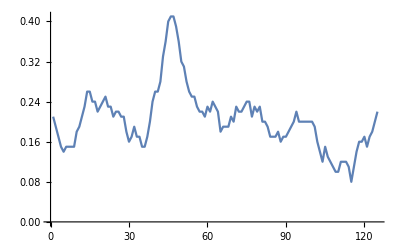

```mathematica
ListPlot[MovingAverage[BinCounts[gasTimes,{0,Max[gasTimes],10}]pulseFactor,10],Joined->True]
```

```mathematica
burntVolume=Total[BinCounts[gasTimes,{0,Max[gasTimes],10}]pulseFactor]
energyContentInBurntGas=burntVolume energyContentInGasPerCubicMeter
price=burntVolume 11 35+burntVolume 30
```

27.6

260.667

11454.

## heat

```mathematica
cycle=1;
```

```mathematica
energyContentDeliveredOnCycles=Total[Quiet[Select[Table[
Select[heatingCumulativeClean[[cycle]],0<#[[1]]&]//#[[-1]][[2]]-#[[1]][[2]]&
,{cycle,1,4}],Positive]]]
```

220

```mathematica
efficiency=100 energyContentDeliveredOnCycles/energyContentInBurntGas
```

84.399

```mathematica
groundTruth={
{3786,5334},
{1585,8044},
{222,6678},
{44,1044}
};(*fűtési, hűtési*)
```

```mathematica
FormatHeatmeterEntry[entry_]:=Module[
{list},
list=StringSplit[entry,""]/.{"-"->-1};
Table[
If[list[[pos]]==-1,
Nothing,
If[
1<pos&&list[[pos-1]]==-1,
-ToExpression[list[[pos]]],
ToExpression[list[[pos]]]
]]
,{pos,1,Length[list]}]
]
```

```mathematica
startDate=DateObject["2023.11.21. 21:45"];
```

```mathematica
timeGranularity="Minute";
```

```mathematica
readout=Map[
Join[
{Round[DateDifferenceInUnits[startDate,DateObject[#[[1]]],timeGranularity],0.25]},
Map[
FormatHeatmeterEntry[#]
&,#[[2;;5]]]
]
&,Map[
StringSplit[#,","]
&,StringSplit[Import[NotebookDirectory[]<>"heatmeter_readouts.csv","Text"],"\n"]]];
```

```mathematica
heatingCumulativeUnclean=Table[DeleteDuplicates[Select[Map[
{#[[1]],ToExpression[StringRiffle[#[[2]],""]]}&,
Select[
Transpose[Transpose[readout][[{1,cycle+1}]]],
MemberQ[#[[2]],-1]==False&
]],#[[2]]-groundTruth[[cycle]][[1]]<1500&]],{cycle,1,4}];
```

```mathematica
heatingCumulativeClean=Table[Table[
If[
10<Abs[heatingCumulativeUnclean[[cycle]][[n]][[2]]-heatingCumulativeUnclean[[cycle]][[n-1]][[2]]],
Nothing,
heatingCumulativeUnclean[[cycle]][[n]]
]
,{n,2,Length[heatingCumulativeUnclean[[cycle]]]}],{cycle,1,4}];
```

```mathematica
heatingDiff=Table[Table[
{Mean[{heatingCumulativeClean[[cycle]][[n]][[1]],heatingCumulativeClean[[cycle]][[n-1]][[1]]}],(heatingCumulativeClean[[cycle]][[n]][[2]]-heatingCumulativeClean[[cycle]][[n-1]][[2]])/(heatingCumulativeClean[[cycle]][[n]][[1]]-heatingCumulativeClean[[cycle]][[n-1]][[1]])}
,{n,2,Length[heatingCumulativeClean[[cycle]]]}],{cycle,1,4}];
```

Power::infy: Infinite expression 1/0. encountered.

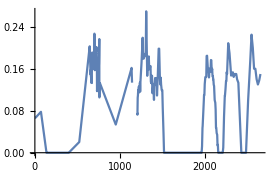
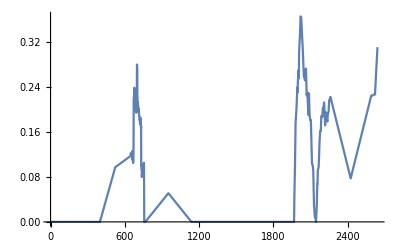
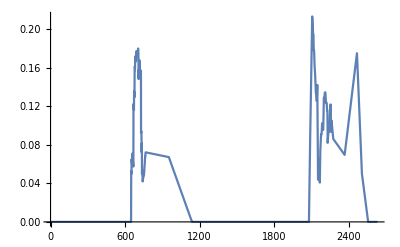
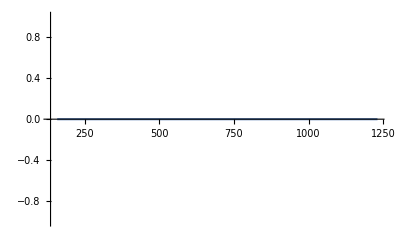

```mathematica
Table[
ListPlot[SparseTimeMovingAverage[heatingDiff[[cycle]],60 1],Joined->True,PlotRange->All]
,{cycle,1,4}]
```

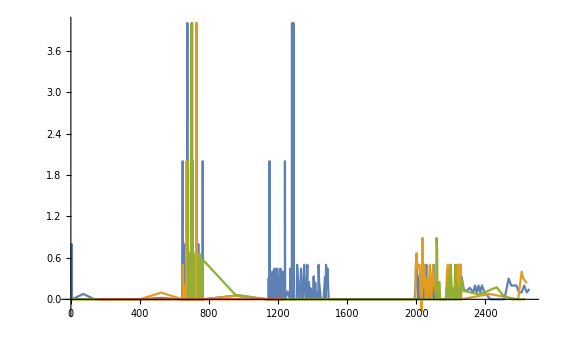

```mathematica
ListPlot[heatingDiff,Joined->True,PlotRange->All]
```